```mathematica
data = Import["E:\\Alessio\\Desktop\\Computazionale\\es3_x^7e^-x\\data_trapezio.txt","Table"];
Trapezio = Take[data][[All,{1,3}]];
DELTATrapezio = Take[data,-500][[All,{2,4}]];
```

```mathematica
data = Import["E:\\Alessio\\Desktop\\Computazionale\\es3_x^7e^-x\\data_simpson.txt","Table"];
Simpson= Take[data][[All,{1,3}]];
DELTASimpson= Take[data,-250][[All,{2,4}]];
```

```mathematica
data= Import["E:\\Alessio\\Desktop\\Computazionale\\es3_x^7e^-x\\data_legendre.txt","Table"];
DELTALegendre = Take[data][[All,{1,3}]];
```

```mathematica
data = Import["E:\\Alessio\\Desktop\\Computazionale\\es3_x^7e^-x\\data_laguerre.txt","Table"];
DELTALaguerre= Take[data][[All,{1,3}]];
```

```mathematica
data =Import["E:\\Alessio\\Desktop\\Computazionale\\es3_x^7e^-x\\data_romberg.txt","Table"];
Romberg1 = Take[data,{8,20}][[All,{1,2}]];
Romberg2 = Take[data,{7,13}][[All,{1,3}]];
Romberg3 = Take[data,{3,9}][[All,{1,4}]];
```

```mathematica
model = a*x^b  ;
```

```mathematica
linetrap=FindFit[DELTATrapezio, model,{a,b},x]
```

{a→472.559,b→2.01203}

```mathematica
linesimp=FindFit[DELTASimpson, model,{a,b},x]
```

{a→351.21039086835353088832994269456054448919,b→4.031133274980106113478852483476182702361}

```mathematica
lineromb1=FindFit[Romberg1, model,{a,b},x]
lineromb2=FindFit[Romberg2, model,{a,b},x]
lineromb3=FindFit[Romberg3, model,{a,b},x]
```

{a→469.0194189441482524014013176429769782097,b→2.010564619805154125355443474818376353027}

{a→376.17028083160110894008969912487034482,b→4.0453544939488594782011066143175406362}

{a→318148.0550632850934161066018905297702,b→6.9585156964554049968971086632199960999}

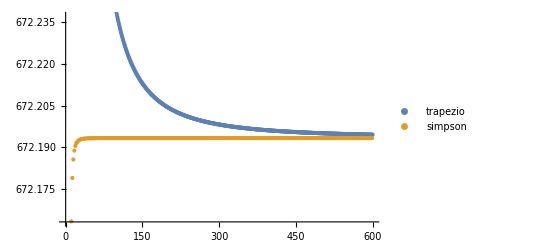

```mathematica
Show[{ListPlot[{Trapezio,Simpson}, PlotLegends->{"trapezio", "simpson"},PlotRange->Automatic],Plot[{model/.linetrap,model/.linesimp},{x,0,1},PlotStyle->Opacity[0.4]]}]
```

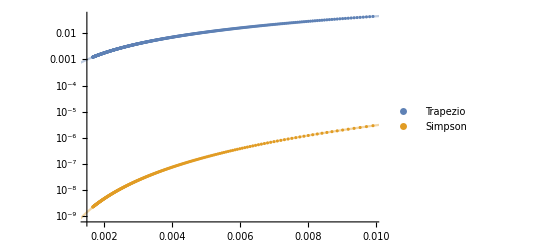

```mathematica
Show[{ListLogPlot[{DELTATrapezio,DELTASimpson}, PlotLegends->{"Trapezio", "Simpson"},PlotRange->All],LogPlot[{model/.linetrap,model/.linesimp},{x,0,0.02},PlotStyle->Opacity[0.4]]}]
```

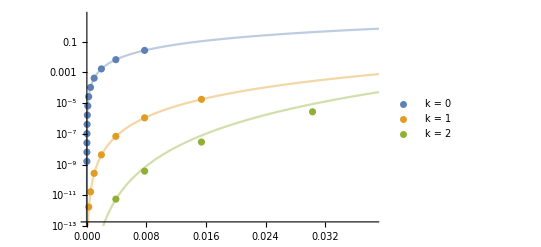

```mathematica
Show[{ListLogPlot[{Romberg1,Romberg2,Romberg3},PlotLegends->{"k = 0","k = 1","k = 2"},PlotRange->Automatic],LogPlot[{model/.lineromb1,model/.lineromb2,model/.lineromb3},{x,0,0.05},PlotStyle->Opacity[0.4]]}]
```

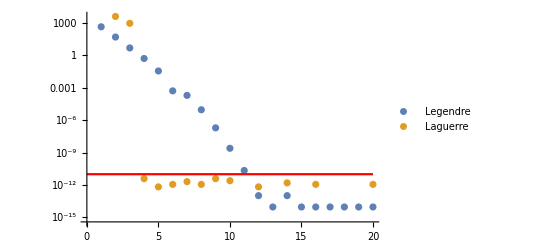

```mathematica
Show[{ListLogPlot[{DELTALegendre, DELTALaguerre}, PlotLegends->{"Legendre", "Laguerre"}, PlotRange->{{0,20},Automatic}],LogPlot[10^(-11),{x,0,20},PlotStyle->Red]}]
```

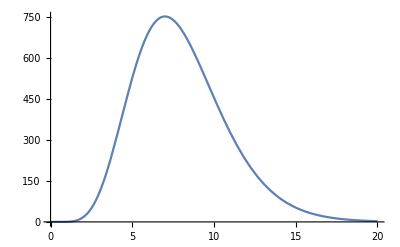

```mathematica
Plot[x^7 * Exp[-x],{x,0,20}]
```

```mathematica
g[x_]= x^7 * Exp[-x]
```

ⅇ^-x x^7

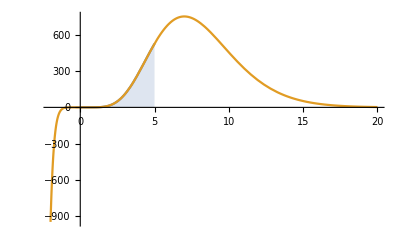

```mathematica
Plot[{If[0<x<5, g[x]],g[x]},{x,-2,20}, Filling->{1->Axis}]
```

```mathematica
Integrate[x^7 * Exp[-x],{x,0,5}]
```

5040-648240/ⅇ^5